# Source of Uncertainty

This notebook demonstrates various properties of the “Source of Uncertainty” PIC module.
Copyright © Terje B. 2006-2015

TODO: Add running data logging to file, for later import/graphing in Octave/R.
See: http://stackoverflow.com/questions/5286640/file-input-output-in-mathematica

```mathematica
(* No need for a long history length eating memory *)
$HistoryLength=1;
(* Clear all previous variable instances *)
ClearAll;

GenerateRandomData[prounds_, pstart_, pfollowbaseline_, pincinterval_,
pvoltref_, prndtime_, pcomplexshape_, dosound_, dolog_] :=
Module[{},
interval = 0.03;
adcValue = 5.0 / pvoltref / 2.0;
curvePos=pstart;
curveShape =0;
maxElements=Ceiling[((Pi-(Pi*-1))/interval*prounds)+(prounds-1)];
modInterval = 0;
randomCurveData = ConstantArray[0, maxElements];
randValue = 0;
counter = 0;
(* If[dolog == True, strOut=OpenWrite["c:/coding/mathematics/SourceOfUncertainty.out.txt"]]; *)
If[prndtime == False, modInterval = 1, modInterval=Ceiling[RandomReal[] * 4.0]];
curveData = ConstantArray[0, maxElements];

For[counter=1, counter <= maxElements, counter++,
(
curveData[[counter]]=Sin[curvePos]; (* / (adcValue);*)

If[pcomplexshape == True,
curveShape = Sin[curvePos] + Cos[curvePos * 4.0],
curveShape = Sin[curvePos]
];

If [Mod[counter,modInterval]==0 ,(* Change pitch *)
(
randValue=((RandomReal[]*Sin[curvePos])/adcValue);

If[pfollowbaseline == False,
randomCurveData[[counter]]=curveShape-randValue,
randomCurveData[[counter]]=randValue
];
If[prndtime==True, modInterval=Ceiling[RandomReal[]*4.0]]
	),
(
If [counter>1,
randomCurveData[[counter]]=randomCurveData[[counter - 1]],

If[pfollowbaseline == False,(* Handle If[counter == 0] here *)
randomCurveData[[counter]]=curveShape-randValue,
randomCurveData[[counter]]=randValue
]
]
)
];
If[pincinterval == True, interval=interval+(prounds/25000.0)]; (*curveInterval;*)
curvePos = curvePos + interval
)
];

(*
If[dolog == True, Write[strOut,randomCurveData]];
Close[strOut];
*)

If[dosound == True,
EmitSound[Play[Sin[Abs[randomCurveData[[1]]]*10000t],{t,0,.01}]]];
{curveData, randomCurveData, maxElements}
]
```

Test the module:

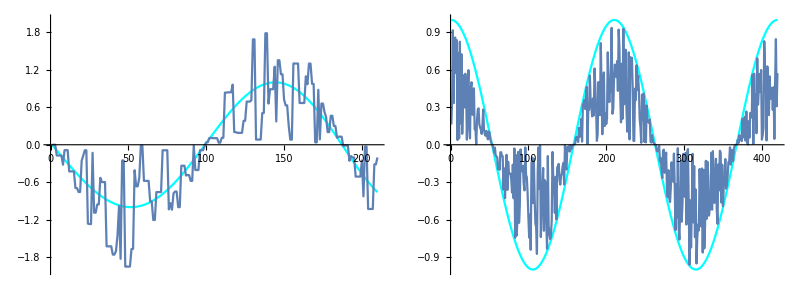

```mathematica
{curveData1, randomData1, maxElements1} = GenerateRandomData[1, -Pi, True, True, 5.0, True, True, False];
{curveData2, randomData2, maxElements2} = GenerateRandomData[2, Pi/2, False, False, 2.5, False, False, False];
Length[randomData1]; Length[curveData1]; randomData1;
g1 = Show[ListLinePlot[curveData1,  PlotStyle->Cyan, PlotRange->{Automatic, {-2, 2}}, PerformanceGoal->"Quality"],
ListLinePlot[randomData1, PerformanceGoal->"Quality"], ImageSize->Scaled[.90]];
g2 = Show[ListLinePlot[curveData2,  PlotStyle->Cyan],ListLinePlot[randomData2, PerformanceGoal->"Quality"], ImageSize->Scaled[.90]];
Grid[{{g1, g2}}, ItemSize->{{25, 25}}, Frame->All, FrameStyle->LightGray]
```

Animate and control the GenerateRandomData module with the MANIPULATE command:

```mathematica
Manipulate[
{curveData, randomData, maxElements} = GenerateRandomData[rounds, start, baseline, incinterval, voltref, rndtime, complexshape, dosound];

g = Show[ListLinePlot[curveData,  PlotStyle->Cyan, PlotRange->{Automatic, {-2, 2}},ImageSize->Scaled[.8], PerformanceGoal->"Quality"],
ListLinePlot[randomData, PerformanceGoal->"Quality"], AxesLabel->{"Phase", "Pitch"}, AspectRatio->.35, ImageSize->Scaled[.98],
GridLines->{None, {-1, 1}}, GridLinesStyle->LightGray];

Grid[{{g}}, ItemSize->{{45, 20}}, Frame->None],
(* NOTE: 2nd cell in Grid is not shown {use: g, g}, but ItemSize is set for it (20) *)

 {{rounds, 1, "Rounds"}, 0.1, 4}, {{voltref, 2.5, "Volt Reference"}, 0.1, 5},
{{start, -Pi, "Start Point"}, -Pi, Pi},{{baseline, True, "Follow Baseline"}, {True, False} }, {{incinterval, True, "Increase Curve Frequency"}, {True, False} },
{{rndtime, False, "Random Time"}, {True, False} },
{{complexshape, True, "Complex Curve Shape"}, {True, False} },
{{dosound, False, "Sound"}, {True, False}},
 SaveDefinitions->True, ControlPlacement->Top]
```

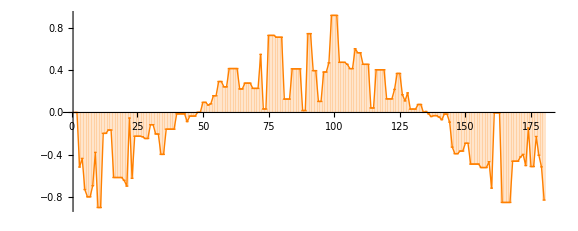

```mathematica
DiscretePlot[randomData[[x]], {x,1,maxElements/1.8}, ExtentSize->Full, Filling->Axis,
AspectRatio->.4,PlotStyle->Orange]
```